# Primary Triangle Shirkins

David Morgan
Winnipeg Canada
dmmorgan@gmail.com

```mathematica
dt[invectorlist_] := Module[
(* draw triangle defined by given list of three 2-vectors *)
	{
	INVECTORLIST = invectorlist
	},
	Show[
		Graphics[{Red, Thick, Line[{INVECTORLIST[[1]], INVECTORLIST[[2]]}]}],
		Graphics[{Green, Thick, Line[{INVECTORLIST[[2]], INVECTORLIST[[3]]}]}],
		Graphics[{Blue, Thick, Line[{INVECTORLIST[[3]], INVECTORLIST[[1]]}]}]
	]
]
```

What follows assumes familiarity with 2D vector rotation and translation. 

Define the equilateral triangle whose apex is the vector [0,1], and translate it such that its lower rightmost vertex is at the origin. This is referenceT, the reference triangle.

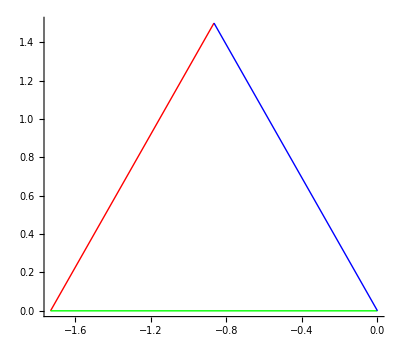

```mathematica
ov = {0,1}; (* original vector *)
ov1 = RotationMatrix[2 Pi / 3] . ov;
ov2 = RotationMatrix[2 Pi / 3] . ov1;
yoffset = Min[#[[2]] & /@ {ov, ov1, ov2}];
xoffset = Max[#[[1]] & /@ {ov, ov1, ov2}];
AA = ov + {-xoffset, -yoffset};
BB = ov1 + {-xoffset, -yoffset};
Origin = ov2 + {-xoffset, -yoffset};
referenceT = dt[{AA,BB,Origin}];
Show[referenceT, Axes -> True]
```

Now, cause two simultaneous, progressive, linked sets of transformations to occur:
	1. the triangle rotates about its Origin, 
	2. the Origin traces an arbitrary path in 2D Cartesian space.
A user-specified number of 2π rotations about the Origin occurs over the course of its traveling the arbitrary path. Here, the path is a circle centered at [0,0].

Specify a radius; create the path, ‘ot,’ origin translation vectors.

2 √3

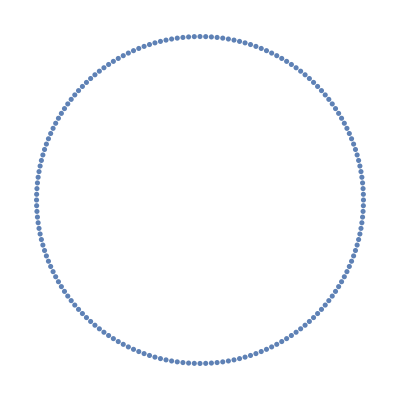

```mathematica
radius =2(Origin - BB)[[1]]

ot = Table[
RotationMatrix[θ ] . {radius, 0}, {θ, 0, 2 Pi-2 Pi / 180, 2 Pi / 180}];ListPlot[ot, Axes -> False, AspectRatio -> 1]
```

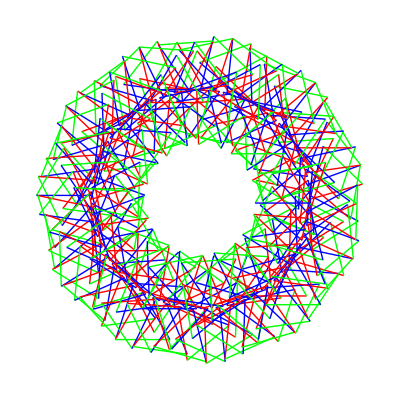

```mathematica
tandr[{origin_,apex_,leftbase_}, totalrotations_,tvtable_]:=Module[
(* translate and rotate *)
{
OO=origin,
AA=apex,
BB=leftbase,
TVTABLE=tvtable (*translation vector table*),
TR=totalrotations, (* over the course of the translation table *)
RTI, (* rotation per increment *)
AAR,BBR,AART,BBRT,OOT, i (* Rotated and Translated vectors; local iterator *)
},
RTI = TR 2 Pi / Length[TVTABLE];
AAR=Table[RotationMatrix[i RTI ].AA,{i,Length[TVTABLE]}];
BBR=Table[RotationMatrix[i RTI ].BB,{i,Length[TVTABLE]}];
AART=Table[AAR[[i]]+TVTABLE[[i]],{i,Length[TVTABLE]}];
BBRT=Table[BBR[[i]]+TVTABLE[[i]],{i,Length[TVTABLE]}];
OOT=Table[OO+TVTABLE[[i]],{i,Length[TVTABLE]}];
Table[dt[{OOT[[i]],AART[[i]],BBRT[[i]]}],{i,Length[TVTABLE]}]
]

tandr[{Origin, AA, BB}, 128,ot];

Show[%]
```

Play around in parameter space.

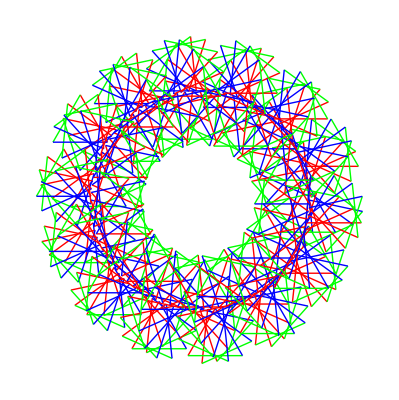

```mathematica
reflength = (Origin - BB)[[1]];
radius =2reflength;

ot = Table[
RotationMatrix[θ ] . {radius, 0}, {θ, 0, 2 Pi-2 Pi / 180, 2 Pi / 180}];
ListPlot[ot, Axes -> False, AspectRatio -> 1];

tandr[{Origin, AA, BB}, 444,ot];
Show[%]
```

Etc.